```mathematica
t=0;
ClearAll[A]
ρ = 1.06;
E0 = 3.7;
nu = 0.34;
l = -18.9;
m = -13.3;
n = -10;
β=3 E0 + 2 l (1-2 nu)^3 + 4 m (1+nu)^2 (1 - 2 nu) + 6 n nu^2;
c = Sqrt[E0/ρ];
R = 5;
```

### Velocity

```mathematica
rho=ρ;
lambda = E0 nu/ ((1+nu) (1 - 2 nu));
mu = E0/(2 (1+nu));
```

```mathematica
(* Pochhammer - Chree, from Boestrom, scaled omega-> omega R/ c and k-> k/R *)
ks = c v k/ R  Sqrt[rho/mu];
kp =  c v k /R  Sqrt[rho/(lambda + 2 mu)];
qs = Sqrt[ks^2 - k^2/ R^2];
qp = Sqrt[kp^2 - k^2 / R^2];
```

```mathematica
DispV = ((ks^2 - 2 kp^2) BesselJ[0, qp R] + 2 qp^2  (D[BesselJ[1, x], x]/. x-> qp R)) (ks^2 - 2 k^2/ R^2) BesselJ[1, qs R] + 4 k^2/ R^2 qp qs BesselJ[1, qp R]  (D[BesselJ[1, x], x]/. x-> qs R) //Simplify;
```

```mathematica
Φ[y_]=y BesselJ[0,y]/BesselJ[1,y];
C0=Sqrt[E0/ρ];
a=(v)^2(1+nu);
b=(1-2nu)(1-nu);
h1=k Sqrt[b a-1];
h2=k Sqrt[2 a-1];
DispV2=(a-1)^2 Φ[h1]-(b a-1)(a-Φ[h2]);
```

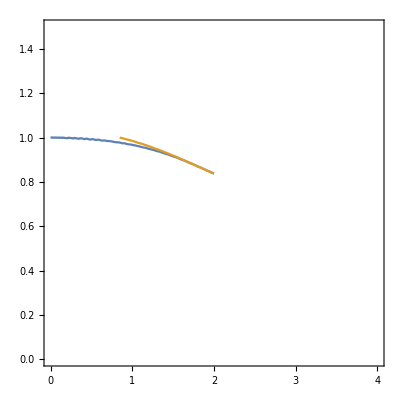

```mathematica
ContourPlot[{DispV==0,DispV2==0},{k, 0, 2}, {v, 0, 1},PerformanceGoal->"Quality",PlotRange->{{0,4},{0,1.5}}]
```

```mathematica
DispVFunc[k_,v_]=DispV;
DispV2Func[k_,v_]=DispV2;
VelCurveLong[k_]:=NSolve[DispVFunc[k,v]==0&&0.7<v<1.001,v]⟦1,1,2⟧;
VelCurveShort[k_]:=NSolve[DispV2Func[k,v]==0&&0.2<v<1.05,v]⟦1,1,2⟧;
```

```mathematica
VelCurve[k_]=If[k<2,VelCurveLong[k],VelCurveShort[k]]
```

If[k<2,VelCurveLong[k],VelCurveShort[k]]

```mathematica
(* Our equation 1 (asymptotic) *)
DD1 =( 4/(nu+1) +  (2 (nu^2 + nu + 1))/(nu+1) k^2)^2 - 4 (4/(nu+1) + k^2) k^2;
Omega3a[k_] = Sqrt[2/(nu+1) + (nu^2 + nu + 1)/(nu+1) k^2 - Sqrt[DD1/4]];
(* Our equation 2 (exact) *)
α1 = ((lambda^2 + 5 lambda mu + 5 mu^2) (3 lambda + 2 mu))/(2 (lambda+mu)^2 (lambda + 2 mu));
α2 = (6 lambda^2 + 21 lambda mu + 14 mu^2)/(2 (lambda+mu) (lambda + 2 mu));
DD2= (4  + α2 k^2)^2 - 4 α1 (4 + k^2) k^2;
Omega4a[k_] = Sqrt[(4 + α2 k^2 - Sqrt[DD2])/(2α1)];
(* DDE *)
Omega2[k_] = Sqrt[((1-(nu/2)  k^2) k^2)/(1 + (nu-1)(nu/2) k^2)];
(* Ostrovsky-Sutin *)
Omega1[k_] =Sqrt[k^2/(1 + (nu^2/2) k^2)];
```

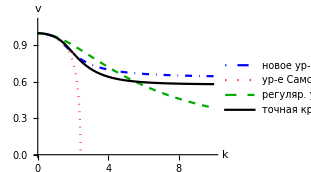

```mathematica
fig=Plot[{Omega4a[k]/k, Omega2[k]/k,Omega1[k]/k,VelCurve[k]},
{k,0.01,10},PlotRange->{0,1.1},
AxesLabel->{"k", "v"},
BaseStyle->{FontSize->14},
PlotStyle->{{Thick, DotDashed,Blue(*,Black*)},{Thick,Dotted,Red(*, Black*)},
{Thick,Dashed,Darker[Green](*, Black*)},
{Black}},
PlotLegends->Placed[{"новое ур-е","ур-е Самсонова",
"регуляр. ур-е Бусс.", "точная кривая"},Right],
ImageSize->230,AspectRatio->3/4
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["DispVelSmall.pdf",fig]
```

DispVelSmall.pdf

### Soliton

```mathematica
B[A_,a_,b_,d_]=Sqrt[(3A β c^2 ρ)/(-4 R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ)))];
V=Sqrt[(A β+3 c^2 ρ)/(3ρ)];
```

```mathematica
u1[A_] =  A Cosh [B[A,(1+nu)/4,(-1-nu-nu^2)/2,(1+nu)/4] (x - V t)]^(-2);
u12[A_]=A Cosh [B[A, (5-5nu-6 nu^2+4 nu^3)/(8(1-nu)),(-7+7nu+2 nu^2)/(8(1-nu)),1/4](x - V t)]^(-2);
u2[A_] =  A Cosh [B[A,0,(1-nu)nu/2,-nu/2] (x - V t)]^(-2);
u3[A_] =  A Cosh [B[A,0,-nu^2/2,0] (x - V t)]^(-2);
```

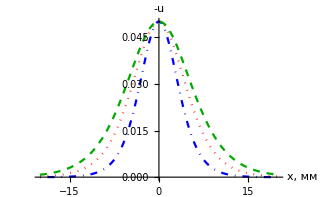

```mathematica
Amp=-0.05;
fig=Plot[{(*-u1[Amp],*) -u12[Amp],-u2[Amp], -u3[Amp]}, {x, -20, 20}, 
(*PlotLegends->LineLegend[{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3],Subscript[u, 4]},LabelStyle->Directive[Black,16]],*)
PlotStyle->{{DotDashed,Blue(*, Black*)},{Dotted,Red(*, Black*)},
{Dashed,Darker[Green](*, Black*)}, {Solid(*,Black*)}},
AxesLabel->{"x, мм",-u},PlotRange->Full,
BaseStyle->{FontSize->14},ImageSize->320
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["FourSolitonsColor.pdf",fig]
```

FourSolitonsColor.pdf

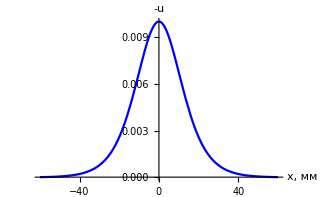

```mathematica
Amp=-0.01;
fig=Plot[{ -u3[Amp]}, {x, -60, 60}, 
PlotStyle->Blue,AxesLabel->{"x, мм",-u},
PlotRange->Full,BaseStyle->{FontSize->14},ImageSize->320
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["SingleSoliton.pdf",fig]
```

SingleSoliton.pdf